If you spot any error (even misspelling) contact me via giovani.garcia@student.kit.edu (cc giovanidvg@gmail.com) .

# A generic handbook for fermionic iDMs

#### Introduction

Here, we follow the particle notation of reference  https://arxiv.org/pdf/XXXXXXXXX, namely:

χ denotes the ground fermionic state with mass mG;
χ^* denotes the excited fermionic state with mass mE (mass splitting Δ mG = mE - mG);
A’ denotes the dark photon (DP) with mass mAp (we assume mAp < mZ, mAp <~ 30 GeV,in order to neglect the Z portal);
h’ denotes the dark Higgs (DH) with mass mHp.
For Majorana fermions, we use “χ^(*)(M)” and, for Dirac fermions,  “χ^(*)(D)” (we assume the interaction coefficients are real in order to have only a decay width for the Dirac case - no difference between particle and anti-particle).

The dark sector couplings are denoted as:
yP for the dark Yukawa coupling and eP for the dark gauge coupling.

The interaction coefficients are denoted as:

dark photon:	α_(_ _) = AvGG , α_(_*) = AvGE , α_(**) = AvEE  , β_(_ _) = BvGG , β_(_*) = BvGE , β_(**) = BvEE .

dark Higgs:	(α̂)_(_ _) = AsGG , (α̂)_(_*) = AsGE , (α̂)_(**) = AsEE  , (β̂)_(_ _) = BsGG , (β̂)_(_*) = BsGE , (β̂)_(**) = BsEE .


The mixing with the SM parameters :
A’ kinetic mixing is denoted by eps and h’ mass mixing angle by tht .


Here, we adopt F_ij=0.



Finally, we use DS to denote dark sector while SM for Standard Model.

## Decay widths and Branching ratios

### Loading phenomenology

```mathematica
nbTemp1=NotebookOpen[StringJoin[NotebookDirectory[],"pheno\\all_decays.nb"]];
```

```mathematica
NotebookEvaluate[nbTemp1];
```

But we use the Central description to be our default in the following (for h’).

```mathematica
NotebookClose[nbTemp1];
```

```mathematica
Clear[nbTemp1];
```

### Loading previous results to be compared

DP into SM figures from https://arxiv.org/pdf/2209.03383.

```mathematica
fig2decaywidthDPsm=-Graphics-;fig2branchingDPsm=-Graphics-;
```

DP into DS previous figures:

```mathematica
PrevFiguBranchingDPdsSwave=-Graphics-;PrevFiguBranchingDPdsPwave1=-Graphics-;PrevFiguBranchingDPdsPwave2=-Graphics-;
```

DH into SM figure from https://arxiv.org/pdf/2305.16169.

```mathematica
fig3p3decaywidthDHsm=-Graphics-;
```

excitedDM into SM via DP figure from https://arxiv.org/pdf/2405.08081.

```mathematica
fig2branchingEdpSM=-Graphics-;
```

excitedDM into SM via DP figure from https://arxiv.org/pdf/2012.08595.

```mathematica
fig8decaywidthEdpSM=-Graphics-;
```

excitedDM into SM via DH figure from https://arxiv.org/pdf/2411.02147.

```mathematica
fig1decaywidthEdhSM=-Graphics-;
```

## Life-times (decay widths)

### A’

The partial decay width into SM final states can be accessed by:

```mathematica
ApDecayWidth["SM:",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"Default"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

where the channels available are (actually some extra channels are available but with different notation - see “pheno\pheno-DP-HS\codes\Acceptances\DP.nb”):

```mathematica
ApSMchannels={"e","μ","τ","π","K","K0","4π","Jets"};
```

More simply, use:

```mathematica
ApDecayWidth["SM:",channel,-1(*-1 will stand for unnecessary info*),-1,mAp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,eps,-1,pheno(*:"Default"*)(*,method_:Automatic*)]
```

The total decay width into SM final states can be accessed by (for the total SM width, we have more final states included than the above mentioned ones - see “pheno\pheno-DP-HS\codes\Acceptances\DP.nb”) :

```mathematica
ApDecayWidth["SM",-1,-1,mAp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,eps,-1,pheno(*:"Default"*)(*,method_:Automatic*)]
```

See “pheno\pheno-DP-HS\codes\Acceptances\DP.nb” for further details on the variable pheno.

The partial decay width into DS final states can be accessed by:

```mathematica
ApDecayWidth["A'→χχ(M)",-1,mG,mAp,-1,eP,-1,AvGG,BvGG,-1,-1,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
ApDecayWidth["A'→χ^*χ^*(M)",mE,-1,mAp,-1,eP,-1,AvEE,BvEE,-1,-1,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
ApDecayWidth["A'→χχ^*",mE,mG,mAp,-1,eP,-1,AvGE,BvGE,-1,-1,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “A’→χχ(D)”.

Or the usual way, e.g.,

```mathematica
ApDecayWidth["A'→χχ(M)",mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"Default"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

The total decay width into DS final states can be accessed by :

```mathematica
ApDecayWidth["DS(M)",mE,mG,mAp,-1,eP,-1,AvGG,BvGG,-1,-1,AvGE,BvGE,-1,-1,AvEE,BvEE,-1,-1,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
```

The TOTAL DECAY WIDTH can be accessed by :

```mathematica
ApDecayWidth["TOTAL(M)",mE,mG,mAp,-1,eP,-1,AvGG,BvGG,-1,-1,AvGE,BvGE,-1,-1,AvEE,BvEE,-1,-1,eps,-1,pheno(*:"Default"*)(*,method_:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “TOTAL(D)”.

The lifetime can be accessed by:

```mathematica
τLLP["A'(M)",mE,mG,mAp,-1,eP,-1,AvGG,BvGG,-1,-1,AvGE,BvGE,-1,-1,AvEE,BvEE,-1,-1,eps,-1,pheno(*:"Default"*)(*,method_:Automatic*)]
```

#### Plotting (Cross-checks)

```mathematica
ApSMchannels
```

```mathematica
NonPerturbativeChannelsAp
```

```mathematica
NonPerturbativeChannelsApForExcited
```

```mathematica
epsPlot=1;
{Show[{ListLogLogPlot[Table[{10^logMaP,ApDecayWidth["SM:","e",-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]},{logMaP,Log10[0.05],Log10[10],0.1}],PlotStyle->Blue,Joined->True,PlotRange->{{0.1,5},{10^-4,2*10^-1}}],ListLogLogPlot[Table[{10^logMaP,If[(temp=ApDecayWidth["SM:","μ",-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[10],0.005}],PlotStyle->LightBlue,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=ApDecayWidth["SM:","τ",-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[10],0.005}],PlotStyle->Orange,Joined->True],LogLogPlot[ApDecayWidth["SM",-1,-1,mAp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1],{mAp,0.07,6},PlotStyle->{Dashed,Gray}],ListLogLogPlot[Table[{10^logMaP,If[(temp=Sum[ApDecayWidth["SM:",channel,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1],{channel,NonPerturbativeChannelsAp}])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[10],0.005}],PlotStyle->Red,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=Sum[ApDecayWidth["SM:",channel,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1],{channel,NonPerturbativeChannelsApForExcited}])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[10],0.005}],PlotStyle->{Dashed,Purple},Joined->True]},ImageSize->Medium],Show[fig2decaywidthDPsm,ImageSize->Medium]}
```

```mathematica
ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1(*,pheno:"Default"*)]
```

```mathematica
ApDecayWidth["A'→χχ(D)",mE_,mG_,mAp_,mHp_,eP_,yP_,Av_,Bv_,As_,Bs_,eps_,tht_,pheno_:"Default",method_:Automatic]
```

```mathematica
ApDecayWidth["A'→χχ(D)",-1,ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,-1,-1]/ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]
```

```mathematica
ApDecayWidth["A'→χχ(M)",-1,ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,-1,-1]/ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]
```

```mathematica
ApDecayWidth["A'→χχ(D)",-1,ParticleMass["e"],0.2,-1,√((4π)/137),-1,0,1,-1,-1,-1,-1]/ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]
```

```mathematica
ApDecayWidth["A'→χχ^*",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,-1,-1]/ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]
```

```mathematica
ApDecayWidth["A'→χ^*χ^*(D)",100ParticleMass["e"],-1,0.2,-1,√((4π)/137),-1,1,0,-1,-1,-1,-1]/ApDecayWidth["SM:","e",-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,epsPlot,-1]
```

```mathematica
ApDecayWidth["DS(D)",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,0.01,-1]
3*ApDecayWidth["SM",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,1,-1]
```

```mathematica
ApDecayWidth["DS(D)",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,0,1,-1,-1,0,1,-1,-1,0,1,-1,-1,0.01,-1]
3*ApDecayWidth["SM",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,1,-1(*,pheno:"Default"*)]
```

```mathematica
ApDecayWidth["TOTAL(D)",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,0.001,-1]
ApDecayWidth["TOTAL(D)",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,1,-1]
4*ApDecayWidth["SM",100ParticleMass["e"],ParticleMass["e"],0.2,-1,√((4π)/137),-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1,1,-1(*,pheno:"Default"*)]
```

### h’

The partial decay width into SM final states can be accessed by:

```mathematica
HpDecayWidth["SM:",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

where the channels available are (actually some extra channels are available but with different notation - see “pheno\pheno-DP-HS\codes\Acceptances\Scalar.nb”):

```mathematica
HpSMchannels={"e","μ","τ","π","K","π0","K0","02π","c","g"};
```

More simply, use:

```mathematica
HpDecayWidth["SM:",channel,-1(*-1 will stand for unnecessary info*),-1,-1,mHp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,tht,pheno(*:"2407.13587-Central"*)(*,method_:Automatic*)]
```

The total decay width into SM final states can be accessed by (for the total SM width, we have more final states included than the above mentioned ones - see “pheno\pheno-DP-HS\codes\Acceptances\Scalar.nb”) :

```mathematica
HpDecayWidth["SM",-1,-1,-1,mHp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,tht,pheno(*:"2407.13587-Central"*)(*,method_:Automatic*)]
```

See “pheno\pheno-DP-HS\codes\Acceptances\Scalar.nb” for further details on the variable pheno.

The partial decay width into DS final states can be accessed by:

```mathematica
HpDecayWidth["h'→χχ(M)",-1,mG,-1,mHp,-1,yP,-1,-1,AsGG,BsGG,-1,-1(*,pheno:"2407.13587-Central"*)(*,method_:Automatic*)]
HpDecayWidth["h'→χ^*χ^*(M)",mE,-1,-1,mHp,-1,yP,-1,-1,AsEE,BsEE,-1,-1(*,pheno:"2407.13587-Central"*)(*,method_:Automatic*)]
HpDecayWidth["h'→χχ^*",mE,mG,-1,mHp,-1,yP,-1,-1,AsGE,BsGE,-1,-1(*,pheno:"2407.13587-Central"*)(*,method_:Automatic*)]
HpDecayWidth["h'→A'A'",-1,-1,mAp,mHp,eP,-1,-1,-1,-1,-1,-1,-1(*,pheno:"2407.13587-Central"*)(*,method_:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “A’→χχ(D)”.

Or the usual way, e.g.,

```mathematica
HpDecayWidth["h'→χχ(M)",mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"Default"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

The total decay width into DS final states can be accessed by :

```mathematica
HpDecayWidth["DS(M)",mE,mG,mAp,mHp,eP,yP,-1,-1,AsGG,BsGG,-1,-1,AsGE,BsGE,-1,-1,AsEE,BsEE,-1,-1(*,pheno:"2407.13587-Central"*)(*,method_:Automatic*)]
```

The TOTAL DECAY WIDTH can be accessed by :

```mathematica
HpDecayWidth["TOTAL(M)",mE,mG,mAp,mHp,eP,yP,-1,-1,AsGG,BsGG,-1,-1,AsGE,BsGE,-1,-1,AsEE,BsEE,-1,tht,pheno(*:"2407.13587-Central"*)(*,method_:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “TOTAL(D)”.

The lifetime can be accessed by:

```mathematica
τLLP["h'(M)",mE,mG,mAp,mHp,eP,yP,-1,-1,AsGG,BsGG,-1,-1,AsGE,BsGE,-1,-1,AsEE,BsEE,-1,tht,pheno(*:"2407.13587-Central"*)(*,method_:Automatic*)]
```

#### Plotting (Cross-checks)

```mathematica
HpSMchannels
```

```mathematica
NonPerturbativeChannelsHp
```

```mathematica
NonPerturbativeChannelsHpForExcited
```

```mathematica
thtPlot=π/2;
{Show[{ListLogLogPlot[Table[{10^logMaP,HpDecayWidth["SM:","e",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"]},{logMaP,Log10[0.05],Log10[30],0.1}],PlotStyle->LightOrange,Joined->True,PlotRange->{{0.1,13},{10^-14,10^-3}}],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","μ",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[30],0.005}],PlotStyle->Orange,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","τ",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[30],0.005}],PlotStyle->Red,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","π0",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"]+HpDecayWidth["SM:","π",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["π0"]],Log10[1.99999],0.005}],PlotStyle->Green,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","K0",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"]+HpDecayWidth["SM:","K",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["K"]],Log10[1.99999],0.005}],PlotStyle->Magenta,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","02π",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["02π"]],Log10[1.99999],0.005}],PlotStyle->LightGreen,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","g",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[2],Log10[30],0.005}],PlotStyle->Purple,Joined->True],ListLogLogPlot[Table[{10^logMaP,If[(temp=HpDecayWidth["SM:","c",-1,-1,-1,10^logMaP,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"])<10^-16,10^-16,temp]},{logMaP,Log10[1.9*ParticleMass["c"]],Log10[30],0.005}],PlotStyle->Blue,Joined->True],LogLogPlot[HpDecayWidth["SM",-1,-1,-1,mAp,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot,"Default"],{mAp,0.07,30},PlotStyle->{Gray}]},ImageSize->Medium],Show[fig3p3decaywidthDHsm,ImageSize->Medium]}
```

```mathematica
HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot(*,pheno:"2407.13587-Central"*)]
```

```mathematica
HpDecayWidth["h'→χχ(D)",-1,ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

```mathematica
HpDecayWidth["h'→χχ(M)",-1,ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

```mathematica
HpDecayWidth["h'→χχ(D)",-1,ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,0,1,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

```mathematica
HpDecayWidth["h'→χχ^*",100ParticleMass["e"],ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

```mathematica
HpDecayWidth["h'→χ^*χ^*(D)",100ParticleMass["e"],-1,-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

Toooooo large “h’→A’A’” ?

```mathematica
HpDecayWidth["h'→A'A'",-1,-1,ParticleMass["e"],0.2,√((4π)/137),-1,-1,-1,-1,-1,-1,-1]
```

```mathematica
HpDecayWidth["h'→A'A'",-1,-1,ParticleMass["e"],0.2,√((4π)/137),-1,-1,-1,-1,-1,-1,-1]/HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot]
```

```mathematica
HpDecayWidth["DS(D)",ParticleMass["e"],ParticleMass["e"],5,0.2,10^-6,ParticleMass["e"]/246,-1,-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,-1]
3*HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot(*,pheno:"2407.13587-Central"*)]
```

```mathematica
HpDecayWidth["DS(D)",100ParticleMass["e"],ParticleMass["e"],5,0.2,10^-6,ParticleMass["e"]/246,-1,-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,0.01]
3*HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot(*,pheno:"2407.13587-Central"*)]
```

```mathematica
HpDecayWidth["DS(D)",ParticleMass["e"],ParticleMass["e"],5,0.2,10^-6,ParticleMass["e"]/246,-1,-1,0,1,-1,-1,0,1,-1,-1,0,1,-1,-1]
3*HpDecayWidth["SM:","e",-1,-1,-1,0.2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,thtPlot(*,pheno:"2407.13587-Central"*)]
```

```mathematica
HpDecayWidth["TOTAL(D)",100ParticleMass["e"],ParticleMass["e"],5,0.2,10^-6,ParticleMass["e"]/246,-1,-1,0,1,-1,-1,0,1,-1,-1,0,1,-1,thtPlot]
HpDecayWidth["TOTAL(D)",100ParticleMass["e"],ParticleMass["e"],5,0.2,10^-6,ParticleMass["e"]/246,-1,-1,1,0,-1,-1,1,0,-1,-1,1,0,-1,thtPlot]
4*HpDecayWidth["SM",100ParticleMass["e"],ParticleMass["e"],0,0.2,-1,ParticleMass["e"]/246,-1,-1,0,1,-1,-1,0,1,-1,-1,0,1,-1,thtPlot(*,pheno:"2407.13587-Central"*)]
```

```mathematica
(HpDecayWidth["h'→χ^*χ^*(D)",100ParticleMass["e"],ParticleMass["e"],5,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]+HpDecayWidth["h'→χχ^*",100ParticleMass["e"],ParticleMass["e"],5,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]+HpDecayWidth["h'→χχ(D)",100ParticleMass["e"],ParticleMass["e"],5,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1])
```

From https://arxiv.org/pdf/1606.07609 -Graphics- and -Graphics-

```mathematica
GammaInv[yχ_,mHp_,mG_]:=(yχ^2 mHp)/(32π)(1-(4 mG^2)/mHp^2)^(3/2)
```

```mathematica
GammaInv[√2 ParticleMass["e"]/246,0.2,ParticleMass["e"]]
HpDecayWidth["h'→χχ(M)",-1,ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]
HpDecayWidth["h'→χχ(D)",-1,ParticleMass["e"],-1,0.2,-1,ParticleMass["e"]/246,-1,-1,1,0,-1,-1]/2
```

Seems to be correct - so maybe some extra things taken into account when computing decays into electrons of the SM.

### χ^*

The partial decay width into SM leptons can be accessed by:

```mathematica
EdecayWidth["fermions",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*"Default"*),method(*:Automatic(NIntegration method)*)]
```

This result is also valid for quarks if perturbative computations are valid. 
The channels available are:

```mathematica
excitedDMfermionicChannels={"e","μ","τ","u","d","c","s","t","b"};
```

For the total decay into leptons, use:

```mathematica
EdecayWidth["leptons",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*"Default"*),method(*:Automatic(NIntegration method)*)]
```

Non-perturbative SM decays can be accessed by:

```mathematica
EdecayWidth["non-perturbative:",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

where the available channels are:

```mathematica
excitedDMsmChannelsNonPerturbative={"π","K","π0","K0","02π","c","g"};
```

However, for some channels we only have the results from one mediator. The channels per mediator are:

```mathematica
excitedDMsmChannelsHpNonPerturbative={"π","K","π0","K0","02π","c","g"};
excitedDMsmChannelsApNonPerturbative={"π","K","K0"};
```

so, when both mediator have the same channels, they contribute together. When only one has, we only show results coming from that mediator.

For the total decay into non-perturbative final states, use:

```mathematica
EdecayWidth["non-perturbative",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

More simply, use:

```mathematica
EdecayWidth["SM:",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

where the available channels are:

```mathematica
excitedDMsmChannels={"e","μ","τ","π","K","π0","K0","02π","c","g"}
```

The total decay width into SM final states can be accessed by:

```mathematica
EdecayWidth["SM",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

All the above neglects contributions from on-shell mediators (e.g., if mHp < mE - mG , we only use the A’ portal for the computation and neglect the contribution from the h’ portal - this can be taken to be the simple 2-body decay χ^*→χh’. If both are on-shell the decay width become just 0).

The partial decay width into DS final states can be accessed by (for DS decays we assume Cos(tht)=1):

```mathematica
EdecayWidth["χ^*→χ h'",mE,mG,-1(*-1 will stand for unnecessary info*),mHp,-1,yP,-1,-1,AsGE,BsGE,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
EdecayWidth["χ^*→χ A'",mE,mG,mAp,-1,eP,-1,AvGE,BvGE,-1,-1,-1,-1(*,pheno:"Default"*)(*,method_:Automatic*)]
EdecayWidth["3χ(M)",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,-1,-1,pheno(*:"Default"*),method(*:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “3χ(D)”.

The 3-body decay χ^*→3χ  neglects contributions from on-shell mediators (e.g., if mHp < mE - mG , we only use A’ for the computation and neglect the contribution from h’ - this can be taken to be the simple 2-body decay χ^*→χh’. If both are on-shell the decay width become just 0).

The total decay width into DS final states can be accessed by :

```mathematica
EdecayWidth["DS(M)",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,-1,-1,pheno(*:"Default"*),method(*:Automatic*)]
```

The TOTAL DECAY WIDTH can be accessed by :

```mathematica
EdecayWidth["TOTAL(M)",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

where “M” stands for the assumption that χ is a Majorana fermion. For Dirac fermions use “D”, e.g., “TOTAL(D)”.

The lifetime can be accessed by:

```mathematica
τLLP["ExcitedDM(M)",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic*)]
```

SM 3-body decays amplitudes can be accessed by :

```mathematica
amplitude2averaged["fermions",fermion,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,m12,m23,pheno(*:"2407.13587-Central"*)]
```

for leptons or high energy quarks.  For DH portal only use “fermions-h’” instead of “fermions” and “fermions-A’” for the DP portal.

Note that m12=(p1+p2)^2 and m23=(p2+p3)^2 are the invariant mass of the particles 1 and 2, and 2 and 3, respectively, squared. We always take particle 1 to be the ground state and particle 3 the anti-particle of the SM “pair”.


While for non-perturbative decays, use

```mathematica
amplitude2averaged["non-perturbative-A':",meson,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,m12,m23,pheno(*:"Default"*)]
```

for charged pions and both charged and neutral kaons in the DP portal, and, in the DH portal, use

```mathematica
amplitude2averaged["non-perturbative-h':",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,m12,m23,pheno(*:"2407.13587-Central"*)]
```

for all DH non-perturbative decay channels. - see all channels above.

DS 3-body decays amplitudes can be accessed by :

```mathematica
amplitude2averaged["3χ(M)","place holder",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,m12,m23,pheno(*:"Default"*)]
```

```mathematica
amplitude2averaged["3χ(D)","place holder",mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,m12,m23,pheno(*:"Default"*)]
```

For DH portal only use “3χ(M)-h’” instead of “3χ(M)” and “3χ(M)-A’” for the DP portal.

#### Plotting (Cross-checks)

```mathematica
excitedDMsmChannels
```

Vector portal:

```mathematica
excitedDMsmChannelsApNonPerturbative
```

```mathematica
{Show[{ListLogLogPlot[ParallelTable[{10^logM,Quiet[1/(EdecayWidth["TOTAL(M)",2*10^logM,10^logM,4*10^logM,10^5,√(4π 0.1),0,1,0,0,0,10^-3,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*5.06*10^13)]},{logM,Log10[0.03],Log10[7],0.1}],PlotStyle->{Black},Joined->True,PlotRange->{{0.05,6.5},{10^-3,10^1}}],ListLogLogPlot[ParallelTable[{10^logM,Quiet[1/(EdecayWidth["SM:","e",2*10^logM,10^logM,4*10^logM,10^5,√(4π 0.1),0,1,0,0,0,10^-3,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*5.06*10^13)]},{logM,Log10[0.03],Log10[7],0.1}],PlotStyle->{Blue,Dashed},Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[1/(EdecayWidth["SM:","μ",2*10^logM,10^logM,4*10^logM,10^5,√(4π 0.1),0,1,0,0,0,10^-3,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*5.06*10^13)]},{logM,Log10[0.03],Log10[7],0.1}],PlotStyle->{Magenta,Dashed},Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[1/(EdecayWidth["non-perturbative-A'",2*10^logM,10^logM,4*10^logM,10^5,√(4π 0.1),0,1,0,0,0,10^-3,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*5.06*10^13)]},{logM,Log10[0.03],Log10[7],0.1}],PlotStyle->{Cyan,Dashed},Joined->True]},ImageSize->Medium],Show[fig8decaywidthEdpSM,ImageSize->Medium]}
```

Scalar portal:

```mathematica
excitedDMsmChannelsHpNonPerturbative
```

```mathematica
{Show[{ListLogLogPlot[Table[{10^logM,Quiet[EdecayWidth["SM:","e",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[21],0.1}],PlotStyle->Orange,Joined->True,PlotRange->{{0.05,20},{10^-34,10^-7}}],ListLogLogPlot[Table[{10^logM,Quiet[EdecayWidth["SM:","μ",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[21],0.01}],PlotStyle->Red,Joined->True],ListLogLogPlot[Table[{10^logM,Quiet[EdecayWidth["SM:","τ",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]*10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[21],0.01}],PlotStyle->Red,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["SM:","π",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]+EdecayWidth["SM:","π0",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[2.2],0.05}],PlotStyle->Green,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["SM:","K",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]+EdecayWidth["SM:","K0",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[2.2],0.05}],PlotStyle->LightBlue,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["SM:","02π",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[2.2],0.05}],PlotStyle->Green,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["SM:","g",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[2.1],Log10[21],0.1}],PlotStyle->Purple,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["SM:","c",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[2.1],Log10[21],0.1}],PlotStyle->Blue,Joined->True],ListLogLogPlot[ParallelTable[{10^logM,Quiet[(EdecayWidth["TOTAL(M)",10^3+10^logM,10^3,10^6,ParticleMass["h"],0,√(4π),0,0,0,1,0,π/4,"Default","MonteCarlo"]) *10^6(*mχ^2*)]},{logM,Log10[0.04],Log10[21],0.1}],PlotStyle->{Dashed,Gray},Joined->True,PlotRange->{{0.05,20},{10^-34,10^-7}}]},ImageSize->250,AspectRatio->1],Show[fig1decaywidthEdhSM,ImageSize->Medium]}
```

```mathematica
ParticleMass["τ"]/246
√((4π)/137)//N
```

```mathematica
EdecayWidth["SM:","τ",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,1,1,1,0,1,0,1,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["SM:","τ",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,1,1,1,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["SM:","τ",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,1,1,1,0,1,0,1,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["SM:","τ",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,10^-2,1,1,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["SM:","τ",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,10^-2,1,1,0,1,0,1,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["SM:","quarks-perturbative",ParticleMass["τ"]+3ParticleMass["τ"],ParticleMass["τ"],10,10,10^-2,1,1,0,1,0,1,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["fermions","c",ParticleMass["τ"]+100,ParticleMass["τ"],0.001,300,0,1,0,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
((√3 ParticleMass["c"])/ParticleMass["τ"])^2*EdecayWidth["fermions","τ",ParticleMass["τ"]+100,ParticleMass["τ"],0.001,300,0,1,0,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),"MonteCarlo"(*:Automatic*)]
```

```mathematica
EdecayWidth["SM:","quarks-perturbative",ParticleMass["τ"]+6,ParticleMass["τ"],10,10,10^-2,1,1,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["SM:","c",ParticleMass["τ"]+6,ParticleMass["τ"],10,10,10^-2,1,1,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),"MonteCarlo"(*:Automatic*)]
```

Dark checks:

```mathematica
EdecayWidth["SM:","e",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],10,10^5,√((4π)/137),0,1,0,0,0,1,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
2*EdecayWidth["3χ(D)",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],10,10^5,√((4π)/137),0,1,0,0,0,1,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["SM:","e",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],10^5,10,0,ParticleMass["e"]/246,0,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
2*EdecayWidth["3χ(D)",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],10^5,10,0,ParticleMass["e"]/246,0,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
3!*EdecayWidth["3χ(M)",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],ParticleMass["e"]/10,10,0,ParticleMass["e"]/246,0,0,1,0,0,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["χ^*→χ h'",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],10^5,ParticleMass["e"]/10,0,1,0,0,0,1,0,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["χ^*→χ A'",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],ParticleMass["e"]/10,10^5,1,0,1,0,0,0,0,0,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["DS(D)",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],2,ParticleMass["e"]/10,1,1,1,0,0,1,1,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
EdecayWidth["SM",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],2,ParticleMass["e"]/10,1,1,1,0,0,1,1,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

```mathematica
EdecayWidth["TOTAL(D)",ParticleMass["e"]+3ParticleMass["e"],ParticleMass["e"],2,ParticleMass["e"]/10,1,1,1,0,0,1,1,π/4,"Default"(*:"2407.13587-Central"*),Automatic(*:Automatic*)]
```

## Branching ratios

### A’

The branching ratio can be simply accessed by:

-for Majorana dark fermions

```mathematica
ApBrachingRatio["M",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"Default"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

-for Dirac dark fermions

```mathematica
ApBrachingRatio["D",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"Default"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

where the channels available are :

```mathematica
ApSMchannels={"e","μ","τ","π","K","K0","4π","Jets"};
ApDSchannels={"A'→χχ(M)","A'→χ^*χ^*(M)","A'→χχ^*"};
ApDSchannels={"A'→χχ(D)","A'→χ^*χ^*(D)","A'→χχ^*"};
```

#### Plotting (Cross-checks)

```mathematica
ApSMchannels
```

```mathematica
NonPerturbativeChannelsAp
```

```mathematica
NonPerturbativeChannelsApForExcited
```

```mathematica
epsPlot=1;
{Show[{ListLogLinearPlot[Table[{10^logMaP,ApBrachingRatio["SM:","e",20+10^3,10^3,10^logMaP,10^5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2]},{logMaP,Log10[0.08],Log10[6],0.005}],PlotStyle->Blue,Joined->True,PlotRange->{{0.1,5},{0,1.05}}],ListLogLinearPlot[Table[{10^logMaP,If[(temp=ApBrachingRatio["SM:","μ",20+10^3,10^3,10^logMaP,10^5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[6],0.005}],PlotStyle->LightBlue,Joined->True],ListLogLinearPlot[Table[{10^logMaP,If[(temp=ApBrachingRatio["SM:","τ",20+10^3,10^3,10^logMaP,10^5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[6],0.005}],PlotStyle->Orange,Joined->True],ListLogLinearPlot[Table[{10^logMaP,If[(temp=Sum[ApBrachingRatio["SM:",channel,20+10^3,10^3,10^logMaP,10^5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2],{channel,NonPerturbativeChannelsAp}])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[6],0.005}],PlotStyle->Red,Joined->True],ListLogLinearPlot[Table[{10^logMaP,If[(temp=Sum[ApBrachingRatio["SM:",channel,20+10^3,10^3,10^logMaP,10^5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2],{channel,NonPerturbativeChannelsApForExcited}])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[6],0.005}],PlotStyle->{Dashed,Purple},Joined->True]},ImageSize->Medium],Show[fig2branchingDPsm,ImageSize->Medium]}
```

```mathematica
ApDSchannels={"A'→χχ(M)","A'→χ^*χ^*(M)","A'→χχ^*"}
```

```mathematica
DefineCoefficients["s-wave niDM"]
```

See the coefficients below:
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE} =

```mathematica
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}
({AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}/.thetaValue//FullSimplify)/.{δy->10^6}
```

```mathematica
{Show[Join[{LogPlot[ApBrachingRatio["M","A'→χχ(M)",(Δm+1)10,10,4*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Red,PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[ApBrachingRatio["M","A'→χχ^*",(Δm+1)10,10,4*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Purple],LogPlot[ApBrachingRatio["M","A'→χ^*χ^*(M)",(Δm+1)10,10,4*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Blue]},{LogPlot[ApBrachingRatio["M","A'→χχ(M)",(Δm+1)10,10,7*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Red,Dotted},PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[ApBrachingRatio["M","A'→χχ^*",(Δm+1)10,10,7*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Purple,Dotted}],LogPlot[ApBrachingRatio["M","A'→χ^*χ^*(M)",(Δm+1)10,10,7*10,10^5,1,0,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Blue,Dotted}]}],ImageSize->Medium],Show[PrevFiguBranchingDPdsSwave,ImageSize->Medium]}
```

```mathematica
ApBrachingRatio["M","A'→χχ^*",(1.975+1)10,10,4*10,10^5,1,0,0,-(500000 1.975)/(500001 (2+1.975)),-2-(1000000 (1000002+1.975))/(500001 (2+1.975)),0,√(1-(250000000000 1.975^2)/(250001000001 (2+1.975)^2)),0,0,1000000 √(1-(250000000000 1.975^2)/(250001000001 (2+1.975)^2)),0,(500000 1.975)/(500001 (2+1.975)),1000002+(500000000000 1.975)/(500001 (2+1.975)),0,10^-10,10^-10]
```

```mathematica
DefineCoefficients["p-wave niDM"]
```

See the coefficients below:
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE} =

```mathematica
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}
({AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}/.thetaValue//FullSimplify)/.{δy->0.5}
```

```mathematica
{Show[Join[{LogPlot[ApBrachingRatio["M","A'→χχ(M)",(Δm+1)10,10,4*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Red,PlotRange->{{0.5,2.5},{5*10^-3,1.5}}],LogPlot[ApBrachingRatio["M","A'→χχ^*",(Δm+1)10,10,4*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Purple],LogPlot[ApBrachingRatio["M","A'→χ^*χ^*(M)",(Δm+1)10,10,4*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Blue]},{LogPlot[ApBrachingRatio["M","A'→χχ(M)",(Δm+1)10,10,7*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Red,Dotted},PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[ApBrachingRatio["M","A'→χχ^*",(Δm+1)10,10,7*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Purple,Dotted}],LogPlot[ApBrachingRatio["M","A'→χ^*χ^*(M)",(Δm+1)10,10,7*10,10^5,1,0,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Blue,Dotted}]}],ImageSize->Medium],Show[PrevFiguBranchingDPdsPwave2,ImageSize->Medium]}
```

```mathematica
ApBrachingRatio["M","e",0.5,0.4,2,100,1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,π/2]
ApBrachingRatio["M","A'→χχ(M)",0.5,0.4,2,100,1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,π/2]
```

```mathematica
ClearCoefficients[]
```

### h’

The branching ratio can be simply accessed by:

-for Majorana dark fermions

```mathematica
HpBrachingRatio["M",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

-for Dirac dark fermions

```mathematica
HpBrachingRatio["D",channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic(integration method only used in 3-body decays)*)]
```

where the channels available are :

```mathematica
HpSMchannels={"e","μ","τ","π","K","π0","K0","02π","c","g"};
HpDSchannels={"h'→χχ(M)","h'→χ^*χ^*(M)","h'→χχ^*","h'→A'A'"};
HpDSchannels={"h'→χχ(D)","h'→χ^*χ^*(D)","h'→χχ^*","h'→A'A'"};
```

#### Plotting

```mathematica
HpSMchannels
```

```mathematica
NonPerturbativeChannelsHp
```

```mathematica
NonPerturbativeChannelsHpForExcited
```

```mathematica
epsPlot=1;
{Show[{ListLogLinearPlot[Table[{10^logMaP,HpBrachingRatio["SM:","e",20+10^3,10^3,10^5,10^logMaP,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2]},{logMaP,Log10[0.08],Log10[6],0.005}],PlotStyle->Blue,Joined->True,PlotRange->{{0.1,5},{0,1.05}}],ListLogLinearPlot[Table[{10^logMaP,If[(temp=HpBrachingRatio["SM:","μ",20+10^3,10^3,10^5,10^logMaP,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[6],0.005}],PlotStyle->Purple,Joined->True],ListLogLinearPlot[Table[{10^logMaP,If[(temp=HpBrachingRatio["SM:","τ",20+10^3,10^3,10^5,10^logMaP,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[6],0.005}],PlotStyle->Orange,Joined->True],ListLogLinearPlot[Table[{10^logMaP,If[(temp=Sum[HpBrachingRatio["SM:",channel,20+10^3,10^3,10^5,10^logMaP,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2],{channel,NonPerturbativeChannelsHp}])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[6],0.005}],PlotStyle->Red,Joined->True]},ImageSize->Medium],Show[fig2branchingDPsm,ImageSize->Medium]}
```

```mathematica
HpBrachingRatio["SM:","μ",20+10^3,10^3,10^5,0.23,1,1,1,1,1,1,1,1,1,1,1,1,1,1,epsPlot,π/2]
```

```mathematica
HpDSchannels
```

```mathematica
DefineCoefficients["s-wave niDM"]
```

See the coefficients below:
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE} =

```mathematica
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}
({AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}/.thetaValue//FullSimplify)/.{δy->10^6}
```

```mathematica
{Show[Join[{LogPlot[HpBrachingRatio["M","h'→χχ(M)",(Δm+1)10,10,10^5,4*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Red,PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[HpBrachingRatio["M","h'→χχ^*",(Δm+1)10,10,10^5,4*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Purple],LogPlot[HpBrachingRatio["M","h'→χ^*χ^*(M)",(Δm+1)10,10,10^5,4*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->Blue]},{LogPlot[HpBrachingRatio["M","h'→χχ(M)",(Δm+1)10,10,10^5,7*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Red,Dotted},PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[HpBrachingRatio["M","h'→χχ^*",(Δm+1)10,10,10^5,7*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Purple,Dotted}],LogPlot[HpBrachingRatio["M","h'→χ^*χ^*(M)",(Δm+1)10,10,10^5,7*10,0,1,0,-(500000 Δm)/(500001 (2+Δm)),-2-(1000000 (1000002+Δm))/(500001 (2+Δm)),0,√(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,0,1000000 √(1-(250000000000 Δm^2)/(250001000001 (2+Δm)^2)),0,(500000 Δm)/(500001 (2+Δm)),1000002+(500000000000 Δm)/(500001 (2+Δm)),0,10^-10,10^-10],{Δm,0,2.5},PlotStyle->{Blue,Dotted}]}],ImageSize->Medium],Show[PrevFiguBranchingDPdsSwave,ImageSize->Medium]}
```

```mathematica
HpBrachingRatio["M","h'→χχ^*",(1.975+1)10,10,10^5,4*10,0,1,0,-(500000 1.975)/(500001 (2+1.975)),-2-(1000000 (1000002+1.975))/(500001 (2+1.975)),0,√(1-(250000000000 1.975^2)/(250001000001 (2+1.975)^2)),0,0,1000000 √(1-(250000000000 1.975^2)/(250001000001 (2+1.975)^2)),0,(500000 1.975)/(500001 (2+1.975)),1000002+(500000000000 1.975)/(500001 (2+1.975)),0,10^-10,10^-10]
```

```mathematica
DefineCoefficients["p-wave niDM"]
```

See the coefficients below:
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE} =

```mathematica
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}
({AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}/.thetaValue//FullSimplify)/.{δy->0.5}
```

```mathematica
{Show[Join[{LogPlot[HpBrachingRatio["M","h'→χχ(M)",(Δm+1)10,10,10^5,4*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Red,PlotRange->{{0.5,2.5},{5*10^-3,1.5}}],LogPlot[HpBrachingRatio["M","h'→χχ^*",(Δm+1)10,10,10^5,4*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Purple],LogPlot[HpBrachingRatio["M","h'→χ^*χ^*(M)",(Δm+1)10,10,10^5,4*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->Blue]},{LogPlot[HpBrachingRatio["M","h'→χχ(M)",(Δm+1)10,10,10^5,7*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Red,Dotted},PlotRange->{{0,2},{5*10^-3,1.5}}],LogPlot[HpBrachingRatio["M","h'→χχ^*",(Δm+1)10,10,10^5,7*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Purple,Dotted}],LogPlot[HpBrachingRatio["M","h'→χ^*χ^*(M)",(Δm+1)10,10,10^5,7*10,0,1,0,-(0.2 (2+Δm))/Δm,2+(0.4 (-0.5+Δm))/Δm,0,0,√(1-(0.04 (2+Δm)^2)/Δm^2),0.5 √(1-(0.04 (2+Δm)^2)/Δm^2),0,0,(0.2 (2+Δm))/Δm,2.5+(0.1 (2+Δm))/Δm,0,10^-10,10^-10],{Δm,0.45,2.6},PlotStyle->{Blue,Dotted}]}],ImageSize->Medium],Show[PrevFiguBranchingDPdsPwave2,ImageSize->Medium]}
```

```mathematica
HpBrachingRatio["M","e",0.5,0.4,100,2,1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,π/2]
HpBrachingRatio["M","h'→χχ(M)",0.5,0.4,100,2,1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,π/2]
```

```mathematica
ClearCoefficients[]
```

### χ^*

The branching ratio can be simply accessed by:

-for Majorana dark fermions

```mathematica
EbrachingRatio["M",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic(integration method)*)]
```

-for Dirac dark fermions

```mathematica
EbrachingRatio["D",channel,mE,mG,mAp,mHp,eP,yP,AvGE,BvGE,AsGE,BsGE,eps,tht,pheno(*:"2407.13587-Central"*),method(*:Automatic(integration method)*)]
```

where the channels available are :

```mathematica
excitedDMfermionicChannels={"e","μ","τ","u","d","c","s","t","b"};
excitedDMdsChannels={"χ^*→χ h'","χ^*→χ A'","3χ(M)"};
excitedDMdsChannels={"χ^*→χ h'","χ^*→χ A'","3χ(D)"};
```

Note that the non-perturbative decays into SM are mediated by two mediators which do not have all the same channels included. The channels included per mediator are :

```mathematica
excitedDMsmChannelsHpNonPerturbative={"π","K","π0","K0","02π","c","g"};
excitedDMsmChannelsApNonPerturbative={"π","K","K0"};
```

When both mediators have the same channel, we include them together in the calculations.

#### Plotting (Cross-checks)

```mathematica
excitedDMsmChannels
```

```mathematica
{Show[{ListLogLogPlot[ParallelTable[{10^logMaP,Quiet[EbrachingRatio["M","e",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]]},{logMaP,Log10[0.18],Log10[9],0.1}],PlotStyle->{Dashed,Red},Joined->True,PlotRange->{{0.2,8},{10^-2,1.01}}],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","μ",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[9],0.1}],PlotStyle->{Dashed,Orange},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","τ",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[9],0.1}],PlotStyle->{Dashed,Purple},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","hadrons-A'",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[9],0.1}],PlotStyle->{Blue},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","π",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[9],0.1}],PlotStyle->{Dashed,Blue},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","K",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]+EbrachingRatio["M","K0",10^logMaP+10^3,10^3,3*10^3,10^9,1,0,1,0,0,0,1,π/2,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[9],0.1}],PlotStyle->{Dashed,Blue},Joined->True]},ImageSize->Medium],Show[fig2branchingEdpSM,ImageSize->Medium]}
```

```mathematica
(*attention too slow figures!!!!*){Show[{ListLogLogPlot[ParallelTable[{10^logMaP,Quiet[EbrachingRatio["M","e",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]]},{logMaP,Log10[0.18],Log10[0.35],0.09}],PlotStyle->{Dashed,Red},Joined->True,PlotRange->{{0.2,8},{10^-2,1.01}}],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","μ",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[9],0.4}],PlotStyle->{Dashed,Orange},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","τ",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["τ"]],Log10[9],0.4}],PlotStyle->{Dashed,Purple},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","π",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]+EbrachingRatio["M","π0",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[3],0.4}],PlotStyle->{Dashed,Blue},Joined->True],ListLogLogPlot[ParallelTable[{10^logMaP,If[(temp=Quiet[EbrachingRatio["M","K",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]+EbrachingRatio["M","K0",10^logMaP+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]])<10^-6,10^-6,temp]},{logMaP,Log10[1.9*ParticleMass["μ"]],Log10[3],0.4}],PlotStyle->{Dashed,Blue},Joined->True]},ImageSize->Medium],Show[fig2branchingEdpSM,ImageSize->Medium]}
```

```mathematica
EbrachingRatio["M","μ",0.25+10^3,10^3,10^9,3*10^3,0,1,0,0,0,1,1,π/4,"Default","MonteCarlo"]
```

```mathematica
excitedDMdsChannels
```

```mathematica
EbrachingRatio["M","χ^*→χ A'",10+10^3,10^3,5,10^9,1,0,1,0,0,0,10^-10,10^-10,"Default","MonteCarlo"]
```

```mathematica
EbrachingRatio["M","χ^*→χ h'",10+10^3,10^3,10^9,5,1,1,1,0,0,1,10^-10,10^-10,"Default","MonteCarlo"]
```

```mathematica
EbrachingRatio["D","3χ(D)",6*10^-5,10^-5,10*10^-5,10*10^-5,1,1,1,0,0,1,10^-10,10^-10,"Default","MonteCarlo"](*take care to not compute for large masses cause it takes too much of time because it is hard to compute the total width since there are too many channels - time expected is 104.64 seconds for very large masses*)//AbsoluteTiming
```

```mathematica
(*the results may not be one because of the montecarlo integration*)
```

## Cleaning useless variables (and/or previous outputs)

```mathematica
Clear[epsPlot,thtPlot,fig2decaywidthDPsm,fig2branchingDPsm,fig3p3decaywidthDHsm,fig2branchingEdpSM,fig8decaywidthEdpSM,fig1decaywidthEdhSM,PrevFiguBranchingDPdsSwave,PrevFiguBranchingDPdsPwave1,PrevFiguBranchingDPdsPwave2,theGraphic1,theGraphic]
```

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"](*cleaning all previous outputs*)
```

## Parameter choices and formulas for standard iDM cases

Example:

```mathematica
DefineCoefficients["s-wave niDM"]
```

Coefficients defined for s-wave niDM ✓

See the coefficients below:
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE} =

```mathematica
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}
{AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE}/.thetaValue//FullSimplify
```

{0,cos(2 θχ),-δy (cos(2 θχ)+1)-2,0,sin(2 θχ),0,0,δy sin(2 θχ),0,-cos(2 θχ),δy (1-cos(2 θχ))+2,0}

{0,-(Δm δy)/((Δm+2) (δy+2)),-(2 δy (Δm+δy+2))/((Δm+2) (δy+2))-2,0,√(1-(Δm^2 δy^2)/((Δm+2)^2 (δy+2)^2)),0,0,δy √(1-(Δm^2 δy^2)/((Δm+2)^2 (δy+2)^2)),0,(Δm δy)/((Δm+2) (δy+2)),(Δm δy^2)/((Δm+2) (δy+2))+δy+2,0}

Other choices are:

```mathematica
DefineCoefficients["p-wave niDM"]
```

```mathematica
DefineCoefficients["i2DM"]
```

Clear all variables with

```mathematica
ClearCoefficients[]:=Module[{},Clear[thetaValue,δy,Δm,θχ,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE];
Print["All coefficients cleared ✓"];
]
```

## Majorana iDM (niDM)

Based on https://arxiv.org/pdf/2201.08409 and https://arxiv.org/pdf/XXXXXX (NEW PAPER to come out)

Their parameters conventions: 
δy = (yL - yR)/yL   .

Their yL → y.
Their Δm → Δ.

### s-wave case

```mathematica
thetaValue={θχ->1/2 ArcCos[- (δy Δ)/((2+δy)(2+Δ))]}
```

vector couplings:

```mathematica
AvGG=0;AvGE=Sin[2 θχ];AvEE=0;BvGG=Cos[2θχ];BvGE=0;BvEE=-Cos[2θχ];
```

scalar couplings:

```mathematica
AsGG=-(2+δy(1+Cos[2θχ]));AsGE=0;AsEE=2+δy(1-Cos[2θχ]);BsGG=0;BsGE=δy Sin[2θχ];BsEE=0;
```

#### Definer

```mathematica
DefineCoefficients["s-wave niDM"]:=Module[{},Clear[thetaValue,δy,Δm,θχ];thetaValue={θχ->1/2 ArcCos[- (δy Δm)/((2+δy)(2+Δm))]};
AvGG=0;AvGE=Sin[2 θχ];AvEE=0;
BvGG=Cos[2θχ];BvGE=0;BvEE=-Cos[2θχ];
AsGG=-(2+δy(1+Cos[2θχ]));AsGE=0;AsEE=2+δy(1-Cos[2θχ]);
BsGG=0;BsGE=δy Sin[2θχ];BsEE=0;

Print["Coefficients defined for s-wave niDM ✓"];
]
```

### p-wave case

```mathematica
theta={θχ->1/2 ArcCos[- (δy (2+Δ))/(Δ(2+δy))]}
```

vector couplings:

```mathematica
AvGG=0;AvGE=0;AvEE=0;BvGG=Cos[2θχ];BvGE=Sin[2 θχ];BvEE=-Cos[2θχ];
```

scalar couplings:

```mathematica
AsGG=2+δy(1+Cos[2θχ]);AsGE=δy Sin[2θχ];AsEE=2+δy(1-Cos[2θχ]);BsGG=0;BsGE=0;BsEE=0;
```

#### Definer

```mathematica
DefineCoefficients["p-wave niDM"]:=Module[{},Clear[thetaValue,δy,Δm,θχ];thetaValue={θχ->1/2 ArcCos[- (δy (2+Δm))/(Δm(2+δy))]};

AvGG=0;AvGE=0;AvEE=0;
BvGG=Cos[2θχ];BvGE=Sin[2 θχ];BvEE=-Cos[2θχ]; 

 AsGG=2+δy(1+Cos[2θχ]);AsGE=δy Sin[2θχ];AsEE=2+δy(1-Cos[2θχ]);
BsGG=0;BsGE=0;BsEE=0;

Print["Coefficients defined for p-wave niDM ✓"];
]
```

## Dirac iDM (i2DM)

Based on https://arxiv.org/pdf/2201.08409 .

Their parameters conventions: 

Their gD → eP.
Their λ → yP.

Their ϕ_D→h’.
Their θ→θχ.

vector couplings:

```mathematica
AvGG=-Sin[ θχ]^2;AvGE=Sin[ θχ]Cos[ θχ];AvEE=-Cos[ θχ]^2;BvGG=0;BvGE=0;BvEE=0;
```

scalar couplings:

```mathematica
AsGG=-Sin[ 2θχ]/√2;AsGE=Cos[ 2θχ]/√2;AsEE=Sin[ 2θχ]/√2;BsGG=0;BsGE=0;BsEE=0;
```

#### Definer

```mathematica
DefineCoefficients["i2DM"]:=Module[{},Clear[thetaValue,θχ];thetaValue={θχ->θχV};
AvGG=-Sin[ θχ]^2;AvGE=Sin[ θχ]Cos[ θχ];AvEE=-Cos[ θχ]^2;BvGG=0;BvGE=0;BvEE=0;

AsGG=-Sin[ 2θχ]/√2;AsGE=Cos[ 2θχ]/√2;AsEE=Sin[ 2θχ]/√2;BsGG=0;BsGE=0;BsEE=0;

Print["Coefficients defined for i2DM ✓"];
]
```

# Appendices

## A: Variables for dark sector particle production at e^+e^- colliders

```mathematica
allProductionChannels={"e^+e^-→ Υ(4s)→ BB→ B K h'","e^+e^-→ Υ(4s)→ BB→ B K h'h'","e^+e^-→ γA'","e^+e^-→ h'A'","e^+e^-→ χχ(M)","e^+e^-→ χχ(D)","e^+e^-→ χχ*","e^+e^-→ χ*χ*(M)","e^+e^-→ χ*χ*(D)","e^+e^-→ γA'h'"};
```

#### Loading phenomenology

```mathematica
nbTemp1=NotebookOpen[StringJoin[NotebookDirectory[],"pheno\\production.nb"]];
```

```mathematica
NotebookEvaluate[nbTemp1];
```

```mathematica
NotebookClose[nbTemp1];
```

```mathematica
Clear[nbTemp1];
```

### Dark Higgs production from B decays

The  B meson branching ratios into final states containing DHs can be accessed by :

```mathematica
BrProduction[channel,mHp,tht,BrHintoHpHp(*the branching ratio of the Higgs into two dark Higgs - see https://arxiv.org/pdf/2503.01760*)]
```

where the channels available are :

```mathematica
BmesonDHchannels={"e^+e^-→ Υ(4s)→ BB→ B K h'"(*independent of BrHintoHpHp*),"e^+e^-→ Υ(4s)→ BB→ B K h'h'"(*independent of tht*)};
```

### Direct production from e^+e^- collisions

The  differential production cross section (as a function of the center of mass angle) can be accessed by :

```mathematica
dσdangleCM[channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,Ecm(*e^+e^- center of mass energy*),angleCM(*0 to π*),GammaAp(*:0*)]
```

where the channels available are :

```mathematica
directChannelsFROMeeCollisions={"e^+e^-→ γA'","e^+e^-→ h'A'","e^+e^-→ χχ(M)","e^+e^-→ χχ(D)","e^+e^-→ χχ*","e^+e^-→ χ*χ*(M)","e^+e^-→ χ*χ*(D)"};
```

The  integrated production cross section can be accessed by :

```mathematica
totalσ[channel,mE,mG,mAp,mHp,eP,yP,AvGG,BvGG,AsGG,BsGG,AvGE,BvGE,AsGE,BsGE,AvEE,BvEE,AsEE,BsEE,eps,tht,Ecm(*e^+e^- center of mass energy*),angle1CM(*0 to π*),angle2CM(*0 to π - angle2CM > angle1CM*),GammaAp(*:0*)]
```

The cross section is integrated from angle1CM to angle2CM and the channels are the same as above (directChannelsFROMeeCollisions).

The  2→3 channels are an exception (since they have more final states parameters). Look at the code in .\pheno\production.nb ...

#### Comparison between channels fixed Γ_A'

We assume a large decay width for the DP ~ 25% mAp

```mathematica
thetaCMmin=32.5*π/180;thetaCMmax=99*π/180;mHpPlot=1;ΔmPlot=1;mApmGratioPlot=5;
PlotStylePerChannel={Cyan,Orange,{Red,Dashed},{Red,Dotted},{Purple,Dashed},{Blue,Dashed},{Blue,Dotted}};
```

Choice 1: small eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√((4π)/137),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,0.25*mApmGratioPlot*x(*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

Choice 2: large eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√(4π 0.5),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,0.25*mApmGratioPlot*x(*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

We assume a very small decay width for the DP ~ 0

```mathematica
thetaCMmin=32.5*π/180;thetaCMmax=99*π/180;mHpPlot=1;ΔmPlot=1;mApmGratioPlot=5;
PlotStylePerChannel={Cyan,Orange,{Red,Dashed},{Red,Dotted},{Purple,Dashed},{Blue,Dashed},{Blue,Dotted}};
```

Choice 1: small eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√((4π)/137),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,0(*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

Choice 2: large eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√(4π 0.5),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,0(*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

#### Comparison between channels using Γ_A'

Loading pheno

```mathematica
If[ChoiceDialog["Loading dark sector decay widths (please cancel if they were already loaded)..."],nbTemp1=NotebookOpen[StringJoin[NotebookDirectory[],"pheno\\all_decays.nb"]];
NotebookEvaluate[nbTemp1];
NotebookClose[nbTemp1];
Clear[nbTemp1];,0;]
```

But we use the Central description to be our default in the following (for h’).

Plotting

```mathematica
thetaCMmin=32.5*π/180;thetaCMmax=99*π/180;mHpPlot=1;ΔmPlot=1;mApmGratioPlot=4;
PlotStylePerChannel={Cyan,Orange,{Red,Dashed},{Red,Dotted},{Purple,Dashed},{Blue,Dashed},{Blue,Dotted}};
```

Choice 1: small eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√((4π)/137),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,ApDecayWidth["TOTAL(M)",(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√((4π)/137),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,"Default"]],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

Choice 2: large eP

```mathematica
Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√(4π 0.5),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,ApDecayWidth["TOTAL(M)",(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√(4π 0.5),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,"Default"](*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,directChannelsFROMeeCollisions//Length}],AxesLabel->{"m_χ","σ"}]
```

#### Comparison with 2→3 processes ERROR ...

```mathematica
thetaCMmin=32.5*π/180;thetaCMmax=99*π/180;mHpPlot=1;ΔmPlot=1;mApmGratioPlot=5;
PlotStylePerChannel={Cyan,Orange,{Red,Dashed},{Red,Dotted},{Purple,Dashed},{Blue,Dashed},{Blue,Dotted}};
```

```mathematica
"e^+e^-→ γA'h'"
```

```mathematica
channels2to2=Show[LogLogPlot[1,{x,0.008,6},PlotRange->{{0.01,5},{10^-14,10^-8}},PlotLegends->LineLegend[PlotStylePerChannel,directChannelsFROMeeCollisions]],Table[LogLogPlot[totalσ[directChannelsFROMeeCollisions[[i]],(1+ΔmPlot)x,x,mApmGratioPlot*x,x,√(4π 0.5),-1,0,1/3,-1,-1,√(1-(1/3)^2),0,-1,-1,0,1/3,-1,-1,10^-3,-1,10(*e^+e^- center of mass energy*),thetaCMmin,thetaCMmax,0.25*mApmGratioPlot*x(*:0*)],{x,0.008,6},PlotStyle->PlotStylePerChannel[[i]],PlotRange->{{0.01,5},{10^-14,10^-8}}],{i,1,((directChannelsFROMeeCollisions//Length)-1)}],AxesLabel->{"m_χ","σ"}]
```

```mathematica
(Log10[0.009]-Log10[5.1])/0.18
```

-15.2963

```mathematica
channels2to3=ListLogLogPlot[ParallelTable[{10^logM,-Quiet[Re[totalσ["e^+e^-→ γA'h'",mApmGratioPlot*10^logM,0.25*mApmGratioPlot*10^logM,10^logM,10,thetaCMmin,thetaCMmax,√(4π 0.5),10^-3,Automatic]]]},{logM,Log10[0.009],Log10[5.1],0.18}],Joined->True,PlotStyle->Black];//AbsoluteTiming
```

{139.476,Null}

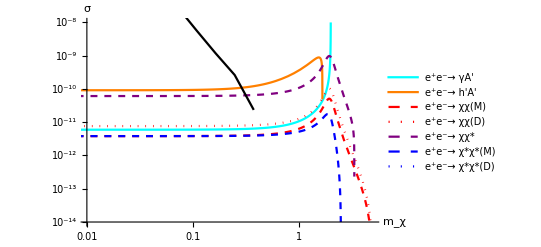

```mathematica
Show[channels2to2,channels2to3]
```

```mathematica
totalσ["e^+e^-→ γA'h'",5,0.1,1,10,0,π,1,1,Automatic]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 199.479+4.47934×10^-14 ⅈ and 236.323 for the integral and error estimates.

0.0000399971